```mathematica
GeneralLinearAnizatropy[α0_,U0_,χ0_,θ0_,β0_,P0_]:= 
Module[{α=α0,U=U0,χ=χ0,θ=θ0,β=β0,P=P0},
(*α - dissipation, α=ν/ω, ω->ω(1+ⅈα)*)
(*U - anizatropy: p^2=4πe^2*n/m, b=eB/(mc), v=p^2/ω^2, u=b^2/ω^2, and with dissipation: v->v(1-ⅈα), u->U(1-ⅈα)*)
(*χ - dimensionless wave vector magnitude; χ=Subscript[k, 0] L, and L=1*) 
(*θ - ngel between wave vector and XOZ*)
(*β - angle between wave vector and magnetic field direction*)
(*P - wave polarisation; 2d-vector*)

(*=====================================================================================================================*)

(*Plasma configuration*)
X=3;(*plasma boundary*)
Δ=0.05;(*smoothing width, in parts of plasma whight*)
n=1/Δ; smoothingFunc=Function[x,(1-(x/X)^(2n))^-1]; v=Function[x,((X^2-x^2)/(X^2-1))*smoothingFunc[x]*(1-ⅈ*α)]; u=U(1-ⅈ*α);
Eps=({{1-v[x]/(1-u), ⅈ(√u)/(1-u)v[x], 0}, {-ⅈ(√u)/(1-u)v[x], 1-v[x]/(1-u), 0}, {0, 0, 1-v[x]}});
(*Plot[{Re[Eps[[3,3]]],Im[Eps[[3,3]]]},{x,-2X,2X}]*)

(*=====================================================================================================================*)

(*Wave configuration*)
A=1;(*wave magnitude*)
k=χ({{Cos[θ]Sin[β]}, {Sin[θ]}, {Cos[θ]Cos[β]}})ᵀ[[1]];(*wave vector*)
Ε=A/Norm[P]({{Cos[β], -Sin[θ]Sin[β]}, {0, Cos[θ]}, {-Sin[β], -Sin[θ]Cos[β]}}).P; (*Electric field (!!!ESCAPE_SEQUENCE!!!)*)
Β=(k×Ε)/χ;(*Magnetic field (!!!ESCAPE_SEQUENCE!!!)*)

(*=====================================================================================================================*)

(*Maxwell equations*)
GeneralSystem = {
(*Ex[x]*Eps[x][[1,1]]+Ey[x]*Eps[x][[1,2]]==kz*By[x]-ky*Bz[x], Bx[x]==ky*Ez[x]-kz*Ey[x],*)
Ey'[x]==ⅈ*χ*(ky*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]+Bz[x]),(*Ey'[x]==ⅈ*χ*(ky*Ex[x]+Bz[x])*)
Ez'[x]==ⅈ*χ*(kz*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]-By[x]),(*Ez'[x]==ⅈ*χ*(kz*Ex[x]-By[x])*)
By'[x]==ⅈ*χ*(ky*(ky*Ez[x]-kz*Ey[x])-Eps[[3,3]]*Ez[x]),(*By'[x]==ⅈ*χ*(ky*Bx[x]-Eps[x][[3,3]]*Ez[x])*)
Bz'[x]==ⅈ*χ*(kz*(ky*Ez[x]-kz*Ey[x])+Eps[[2,1]]*(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]+Eps[[2,2]]*Ey[x])(*Bz'[x]==ⅈ*χ*(kz*Bx[x]+Eps[x][[2,1]]*Ex[x]+Eps[x][[2,2]]*Ey[x])*)
}/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ};

GeneralInitials = {Ey[2X]==Ε[[2]],Ez[2X]==Ε[[3]],By[2X]==Β[[2]],Bz[2X]==Β[[3]]};
Sol=NDSolveValue[{GeneralSystem,GeneralInitials},{Ey,Ez,By,Bz},{x,-2X,2X}];

(*=====================================================================================================================*)

(*Polarisation rotations*)
Transmitted=If[P[[1]]==0,Conjugate[P[[2]]]/Abs[P[[2]]],Conjugate[P[[1]]]/Abs[P[[1]]]]({{P[[1]]/Norm[P]}, {P[[2]]/Norm[P]}})ᵀ[[1]];(*Transmitted wave*)
IW=(({{Cos[β], 0, -Sin[β]}, {-Sin[β]Sin[θ], Cos[θ], -Cos[β]Sin[θ]}}).({{(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]}, {Ey[x]}, {Ez[x]}}))ᵀ[[1]]/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ,Ey[x]->Sol[[1]][x],Ez[x]->Sol[[2]][x],By[x]->Sol[[3]][x],Bz[x]->Sol[[4]][x]};
IP=({{a/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==IW[[1]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[IW[[1]],x]/.x->(-2X)},{a,b}][[1]]}, {a/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==IW[[2]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[IW[[2]],x]/.x->(-2X)},{a,b}][[1]]}})ᵀ[[1]];
Initial=If[IP[[1]]==0,Conjugate[IP[[2]]]/Abs[IP[[2]]],Conjugate[IP[[1]]]/Abs[IP[[1]]]]({{IP[[1]]/Norm[IP]}, {IP[[2]]/Norm[IP]}})ᵀ[[1]];(*Initial wave*)
RW=(({{Cos[π-β], 0, -Sin[π-β]}, {-Sin[π-β]Sin[-θ], Cos[-θ], -Cos[π-β]Sin[-θ]}}).({{(kz*By[x]-ky*Bz[x]-Ey[x]*Eps[[1,2]])/Eps[[1,1]]}, {Ey[x]}, {Ez[x]}}))ᵀ[[1]]/.{kx->k[[1]]/χ,ky->k[[2]]/χ,kz->k[[3]]/χ,Ey[x]->Sol[[1]][x],Ez[x]->Sol[[2]][x],By[x]->Sol[[3]][x],Bz[x]->Sol[[4]][x]};
RP=({{b/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==RW[[1]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[RW[[1]],x]/.x->(-2X)},{a,b}][[1]]}, {b/.NSolve[{a*Exp[ⅈ*k[[1]](-2X)]+b*Exp[-ⅈ*k[[1]](-2X)]==RW[[2]]/.x->(-2X),ⅈ*k[[1]]a*Exp[ⅈ*k[[1]](-2X)]-ⅈ*k[[1]]b*Exp[-ⅈ*k[[1]](-2X)]==D[RW[[2]],x]/.x->(-2X)},{a,b}][[1]]}})ᵀ[[1]];
Reflected=If[RP[[1]]==0,Conjugate[RP[[2]]]/Abs[RP[[2]]],Conjugate[RP[[1]]]/Abs[RP[[1]]]]({{RP[[1]]/Norm[RP]}, {RP[[2]]/Norm[RP]}})ᵀ[[1]];(*Reflected wave*)
(*Dissipation*)
Dissipation=1-Norm[RP]/Norm[IP];

(*=====================================================================================================================*)

{Eps,k,Sol,Initial,Reflected,Transmitted,Dissipation}

]
```

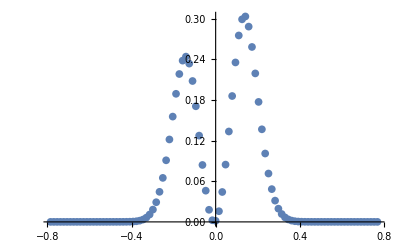

```mathematica
DissipationFromΘ={};
begining=-π/4;end=π/4;nstep=100;
ProgressIndicator[Dynamic[(Θ-begining)/(end-begining)]]
For[Θ=begining,Θ<end,Θ+=(end-begining)/nstep,
DissipationFromΘ=Append[DissipationFromΘ,{Θ,GeneralLinearAnizatropy[0.000001,0.000001,30,Θ,π/2,{0,1}][[7]]}];
];
ListPlot[DissipationFromΘ,PlotRange->Full]
```